```mathematica
(*A[u] = a (1-ζ u (4-3u));*)
ω = x - ϵ t;
u = ϕ[ω];
LHS = D[u, t] - D[A[u] D[u, x], x]
FullSimplify[LHS]
```

-ϵ ϕ'[x-t ϵ]-A'[ϕ[x-t ϵ]] ϕ'[x-t ϵ]^2-A[ϕ[x-t ϵ]] ϕ''[x-t ϵ]

-ϕ'[x-t ϵ] (ϵ+A'[ϕ[x-t ϵ]] ϕ'[x-t ϵ])-A[ϕ[x-t ϵ]] ϕ''[x-t ϵ]

DSolve::argmu: DSolve called with 1 argument; 3 or more arguments are expected.

DSolve[-ϵ ϕ'[x-t ϵ]-A'[ϕ[x-t ϵ]] ϕ'[x-t ϵ]^2-A[ϕ[x-t ϵ]] ϕ''[x-t ϵ]==0]

```mathematica
A[ϕ]
ϕ[ω]
FullSimplify[DSolve[-ϵ D[ϕ[ω], ω] == D[A[ϕ[ω]]D[ϕ[ω], ω], ω], ϕ,ω] ]
```

A[ϕ]

ϕ[ω]

{{ϕ→Function[{ω},InverseFunction[∫_1^#1 1/(C[1]/A[K[1]]-(ϵ K[1])/A[K[1]])ⅆK[1]&][ω+C[2]]]}}

```mathematica
-ϵ D[ϕ, ω] - D[A[ϕ]D[ϕ, ω]]
```

0

```mathematica
A[u] = a (1-ζ u (4-3u));
ξ = ϕ;
temp = Apart[(a (1-ζ ξ (4-3ξ)))/(ϵ μ-ϵ ξ)];
new = Integrate[temp, ξ]
FullSimplify[new]
FullSimplify[D[new, ϕ]]
```

(a (-1/2 ζ ϕ (-8+6 μ+3 ϕ)+(-1+ζ (4-3 μ) μ) Log[-μ+ϕ]))/ϵ

(a (-1/2 ζ ϕ (-8+6 μ+3 ϕ)+(-1+ζ (4-3 μ) μ) Log[-μ+ϕ]))/ϵ

(a (1+ζ ϕ (-4+3 ϕ)))/(ϵ (μ-ϕ))

```mathematica
ω[ϕ_, ζ_, μ_, ϵ_] :=(ϵ ζ (-6 μ+ϵ (8-3 ϕ)) ϕ-2 (ϵ^2-4 ϵ ζ μ+3 ζ μ^2) Log[μ-ϵ ϕ])/(2 ϵ^3);
Manipulate[Plot[ω[ϕ, ζ, μ, ϵ], {ϕ, 0, 1}, PlotRange->All], {ζ, -1, 1}, {μ, -1, 1}, {ϵ, -1, 1}]
```

```mathematica
ω=(a(ϵ ζ (-6 μ+ϵ (8-3 ϕ)) ϕ-2 (ϵ^2-4 ϵ ζ μ+3 ζ μ^2) Log[μ-ϵ ϕ]))/(2 ϵ^3);
FullSimplify[D[ω, ϕ]]
```

(a (1+ζ ϕ (-4+3 ϕ)))/(μ-ϵ ϕ)

```mathematica
Expand[(1+ζ ϕ (-4+3 ϕ))]
```

1-4 ζ ϕ+3 ζ ϕ^2

```mathematica
FullSimplify[Reduce[(a (1+ζ ϕ (-4+3 ϕ)))/(ϵ (μ-ϕ))>0&&a>0&&ζ<1&&μ ∈ Reals&&ϵ >0&&0<ϕ<1]]
```

a>0&&ϵ>0&&((ζ<1&&((ζ>1/(4 ϕ-3 ϕ^2)&&ϕ<1&&((3 μ>1&&μ<ϕ&&μ≤1)||(3 ϕ>1&&3 μ≤1)))||(ϕ>0&&((μ>0&&μ>ϕ&&3 μ≤1)||(3 μ>1&&3 ϕ≤1)))))||(3 ϕ>1&&ζ<1/(4 ϕ-3 ϕ^2)&&((μ>1&&ϕ<1)||(3 μ>1&&μ>ϕ&&μ≤1))))

```mathematica
Solve[(1+ζ ϕ (-4+3 ϕ))==0, ϕ]
```

{{ϕ→(2 ζ-√(-3 ζ+4 ζ^2))/(3 ζ)},{ϕ→(2 ζ+√(-3 ζ+4 ζ^2))/(3 ζ)}}

```mathematica
Manipulate[Plot[1+ζ ϕ (-4+3 ϕ), {ϕ, 0, 1}], {ζ, -1, 1}]
```

```mathematica
Manipulate[Plot[ϵ^-1(1/2 ζ ϕ (8-6μ ϵ-3ϕ)-(1-ζ(4-3μ ϵ)μ ϵ)Log[ϕ-μ ϵ]), {ϕ, 0, 1}, PlotRange->All], {μ, -1, 1}, {ζ, 0, 1}, {ϵ, 0, 1}]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
FullSimplify[-a (1-ζ ϕ (4-3ϕ))/D[a ϵ^-1(1/2 ζ ϕ (8-3ϕ)-Log[ϕ]), ϕ]]
```

ϵ ϕ

```mathematica
Solve[a ϵ^-1(1/2 ζ ϕ (8-3ϕ)-Log[ϕ])==ω, ϕ]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[(a (1/2 ζ (8-3 ϕ) ϕ-Log[ϕ]))/ϵ==ω,ϕ]

```mathematica
DSolve[ω ϕ'[ω]==-2D[a (1-ζ ϕ [ω](4-3ϕ[ω])) ϕ'[ω], ω], ϕ[ω], ω]
```

DSolve[ω ϕ'[ω]==-2 (a ϕ'[ω] (-ζ (4-3 ϕ[ω]) ϕ'[ω]+3 ζ ϕ[ω] ϕ'[ω])+a (1-ζ (4-3 ϕ[ω]) ϕ[ω]) ϕ''[ω]),ϕ[ω],ω]

```mathematica
FullSimplify[ω ϕ'[ω]-2D[a (1-ζ ϕ [ω](4-3ϕ[ω])) ϕ'[ω], ω]]
```

ω ϕ'[ω]+4 a ζ (2-3 ϕ[ω]) ϕ'[ω]^2-2 a (1+ζ ϕ[ω] (-4+3 ϕ[ω])) ϕ''[ω]

NDSolve::berr: The scaled boundary value residual error of 739.962 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

{{ϕ[ω]→InterpolatingFunction[{{-10., 10.}}, <>][ω]}}

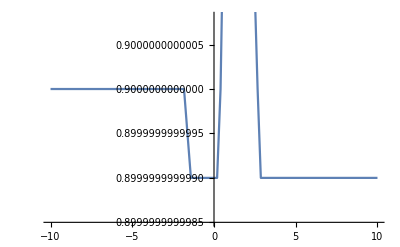

```mathematica
ζ = 0.6;a=1;
s=NDSolve[{ω ϕ'[ω]==-2D[a (1-ζ ϕ [ω](4-3ϕ[ω])) ϕ'[ω], ω], ϕ[0]==0.9, ϕ'[10]==-0.1}, ϕ[ω], {ω, -10, 10}]
Plot[Evaluate[ϕ[ω]/.s] ,{ω, -10, 10}]
```

```mathematica
ω = f[ξ];
ω ϕ'[ω]-2D[a (1-ζ ϕ [ω](4-3ϕ[ω])) ϕ'[ω], ω]
```

f[ξ] ϕ'[f[ξ]]-2 (a ϕ'[f[ξ]] (-ζ (4-3 ϕ[f[ξ]]) ϕ'[f[ξ]]+3 ζ ϕ[f[ξ]] ϕ'[f[ξ]])+a (1-ζ (4-3 ϕ[f[ξ]]) ϕ[f[ξ]]) ϕ''[f[ξ]])

```mathematica
D[1/D[ω[ξ], ξ], ξ]
```

-ω''[ξ]/ω'[ξ]^2